```mathematica
foo=Import["D:\\Dokumente\\Dissertation\\Code\\python\\ptsne-pytorch\\projected_output_test.csv", "Table"];
```

```mathematica
data=Partition[foo,60000];
```

```mathematica
vectors=Thread[{data⟦3⟧,data⟦4⟧}];
```

```mathematica
Graphics[{Opacity[0.3],Arrowheads[0.02],Arrow/@vectors⟦;;2000⟧},ImageSize->1500]
```

```mathematica
x1=data⟦2⟧;
x2=data⟦3⟧;
```

```mathematica
x1n=MapThread[Rescale,{x1ᵀ,MinMax/@(x2ᵀ),{{-1,1},{-1,1}}}]ᵀ;
```

```mathematica
x2n=MapThread[Rescale,{x2ᵀ,MinMax/@(x2ᵀ),{{-1,1},{-1,1}}}]ᵀ;
```

```mathematica
fn=x2n-x1n;
```

```mathematica
vectorsn=Thread[{x1n,x1n+fn}];
```

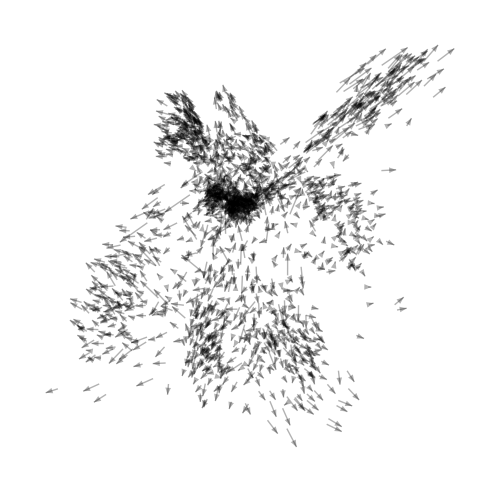

```mathematica
Graphics[{Opacity[0.3],Arrowheads[0.02],Arrow/@vectorsn⟦;;2000⟧},ImageSize->500]
```

```mathematica
grid=Flatten[Table[{i,j},{i,-1,1,0.01},{j,-1,1,0.01}],1];
```

```mathematica
gauss[x0_,x_,f_]:=
```

```mathematica
PDF[BinormalDistribution[{0.1,0.1},0],{xx,yy}]
```

15.9155 ⅇ^(1/2 (0.-100. xx^2-100. yy^2))